```mathematica
V[x_,q_,n_]:=q(n(n+1))/(2 Cosh[x]^2)
```

```mathematica
k[x_,q_,n_]:=√(2(En-V[x,q,n]))
```

```mathematica
Subscript[M, c][x_,q_,n_,dx_]:={{E^(I k[x,q,n]*dx),0},{0,E^(-I k[x,q,n]*dx)}}
```

```mathematica
Subscript[M, s][x_,q_,n_,dx_]:=0.5*{{1+k[x,q,n]/k[x+dx,q,n],1-k[x,q,n]/k[x+dx,q,n]},{1-k[x,q,n]/k[x+dx,q,n],1+k[x,q,n]/k[x+dx,q,n]}}
```

```mathematica
listmultiplier[list_,partitionwidth_:5]:=NestWhile[Dot@@@Partition[#,partitionwidth,partitionwidth,1,{}]&,list,Dimensions[#][[1]]>1&][[1]]
```

```mathematica
BigM[q_,n_,dx_]:=Reverse@Table[Subscript[M, s][x,q,n,dx].Subscript[M, c][x,q,n,dx],{x,-3,3,dx}]//N;
```

```mathematica
Mlist1=BigM[1,1,0.005];Mlist2=BigM[-1,1,0.005];
```

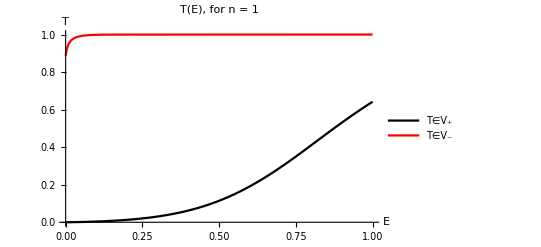

```mathematica
Plot[{1/(ComplexExpand@Abs@listmultiplier[Mlist1,10][[2]][[2]])^2,1/(ComplexExpand@Abs@listmultiplier[Mlist2,10][[2]][[2]])^2},{En,0,1},PlotRange->All,PlotStyle->{Black,Red},PlotLegends->{"T∈V_+","T∈V_-"},AxesLabel->{"E","T"},PlotLabel->"T(E), for n = 1"]
```